```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
(*Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];Format[mu3]:=Subscript[μ,3];Format[mu0]:=Subscript[μ,0];
Format[R1]:=Subscript[R,1];Format[R2]:=Subscript[R,2];Format[R3]:=Subscript[R,3];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[ga1]:=Subscript[γ,1];Format[ro12]:=Subscript[ρ,12];Format[ro23]:=Subscript[ρ,23];Format[ga2]:=Subscript[γ,2];Format[s0]:=Subscript[s,0];
Format[th]:=θ;
Format[La]:=Λ;
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i3]:=Subscript[i,3];
Format[i12]:=Subscript[i,12];*)

cLog={be1->0,be2->0,ga1->0,ga2->0,b->r*s*(1-s/s0),mu0->0};
cbg={be1->0,be2->0,ga1->0,ga2->0};
cbe={be1->0,be2->0};cb=b->s0 mu0;cga={ga1->0,ga2->0};
cet={et1->s13 mu1 mu3 (R1-R3)/((s0-s13)mu0 s0),
et2->s23 mu2 mu3 (R2-R3)/((s0-s23)mu0 s0)};
cmu={mu2 ->mu,mu3->mu,mu1 ->mu,mu0->mu};
c3={i12->0};c2={i2->0};c1={i1->0};cb=b->r*s*(1-s/s0);
RN={0->"S","S"->0,"S"+"I1"->2*"I1","I1"->0,"I1"+"I2"->2*"I2","I2"->0,"I2"+"I3"->2*"I3","I3"->0};
rts={La,mu0*s,be1*s*i1,mu1*i1,ro12*i1*i2,mu2*i2,ro23*i2*i3,mu3*i3};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
res = findCores[RN,2];
res["all"]
```

Load CRNT

reactions and transitions: (0→S | La
S→0 | mu0 s
I1+S→2 I1 | be1 i1 s
I1→0 | i1 mu1
I1+I2→2 I2 | i1 i2 ro12
I2→0 | i2 mu2
I2+I3→2 I3 | i2 i3 ro23
I3→0 | i3 mu3)

{<|T→{s,i1},intReacIdx→{1,3},details→<|t→1/2,flux→<|1→1,3→1/2|>|>|>}

```mathematica
RN3 = {0 -> "S", "S" -> 0, 
       "S" + "I1" -> 2*"I1", "I1" -> 0,
       "S" + "I2" -> 2*"I2", "I2" -> 0};
res = findCores[RN3, 3];res["all"]
```

{<|T→{s,i1},intReacIdx→{1,3},details→<|t→1/2,flux→<|1→1,3→1/2|>|>|>,<|T→{s,i2},intReacIdx→{1,5},details→<|t→1/2,flux→<|1→1,5→1/2|>|>|>,<|T→{s,i1,i2},intReacIdx→{1,3,5},details→<|t→1/3,flux→<|1→1,3→1/3,5→1/3|>|>|>}

Load CRNT

reactions and transitions: (0→S | La
S→0 | mu0 s
I1+S→2 I1 | be1 i1 s
I1→0 | i1 mu1
I1+I2→2 I2 | i1 i2 ro12
I2→0 | i2 mu2
I2+I3→2 I3 | i2 i3 ro23
I3→0 | i3 mu3)

Minimal siphons: {T_1={i1},T_2={i2},T_3={i3}}

IGMS edges: {1→2,2→3}

IGMS is acyclic (no cycles found)

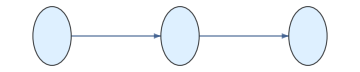

siphons are{{i1},{i2},{i3}} edges are{1→2,2→3}  DFE is{s→La/mu0,i1→0,i2→0,i3→0} repr. functions  {(be1 s)/mu1}

K=((be1 s)/mu1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)F=(be1 s | 0 | 0
0 | 0 | 0
0 | 0 | 0)V=(mu1 | 0 | 0
0 | mu2 | 0
0 | 0 | mu3)

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

General::stop: Further output of LinearProgramming::lpsnf will be suppressed during this calculation.

<|species→{s,i1,i2,i3},tested→14,allResults→{<|T→{i1},isCore→False,reason→no internal reactions|>,<|T→{i2},isCore→False,reason→no internal reactions|>,<|T→{i3},isCore→False,reason→no internal reactions|>,<|T→{s,i1},isCore→True,intReacIdx→{1,3},details→<|isCore→True,t→1/2,flux→<|1→1,3→1/2|>,growth→{1/2,1/2}|>|>,<|T→{s,i2},isCore→False,intReacIdx→{1},details→<|isCore→False,reason→growth not strictly positive,t→0,v→{1/100000000},growth→{1/100000000,0}|>|>,<|T→{s,i3},isCore→False,intReacIdx→{1},details→<|isCore→False,reason→growth not strictly positive,t→0,v→{1/100000000},growth→{1/100000000,0}|>|>,<|T→{i1,i2},isCore→False,intReacIdx→{5},details→<|isCore→False,reason→LP failed|>|>,<|T→{i1,i3},isCore→False,reason→no internal reactions|>,<|T→{i2,i3},isCore→False,intReacIdx→{7},details→<|isCore→False,reason→LP failed|>|>,<|T→{s,i1,i2},isCore→True,intReacIdx→{1,3,5},details→<|isCore→True,t→1/3,flux→<|1→1,3→2/3,5→1/3|>,growth→{1/3,1/3,1/3}|>|>,<|T→{s,i1,i3},isCore→False,intReacIdx→{1,3},details→<|isCore→False,reason→growth not strictly positive,t→0,v→{1/200000000,1/200000000},growth→{0,1/200000000,0}|>|>,<|T→{s,i2,i3},isCore→False,intReacIdx→{1,7},details→<|isCore→False,reason→growth not strictly positive,t→0,v→{1/100000000,0},growth→{1/100000000,0,0}|>|>,<|T→{i1,i2,i3},isCore→False,intReacIdx→{5,7},details→<|isCore→False,reason→LP failed|>|>,<|T→{s,i1,i2,i3},isCore→True,intReacIdx→{1,3,5,7},details→<|isCore→True,t→1/4,flux→<|1→1,3→3/4,5→1/2,7→1/4|>,growth→{1/4,1/4,1/4,1/4}|>|>},cores→{<|T→{s,i1},isCore→True,intReacIdx→{1,3},details→<|isCore→True,t→1/2,flux→<|1→1,3→1/2|>,growth→{1/2,1/2}|>|>}|>

```mathematica
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
{edg,cyc,graph}=IGMS[RN, mSi];
Print["siphons are",mSi," edges are",edg,"  DFE is",E0," repr. functions  ",R0A];F=ng[[2]];V=ng[[3]];
Print["K=",K//MatrixForm,"F=",F//MatrixForm,"V=",V//MatrixForm];
```

```mathematica
?EpidCRN`*
```